```mathematica
(* translation operators *)
U[k_,kp_, Ν_]:=N[Sum[1/Ν Exp[I((2π)/Ν)((kp-k+1) n+1/2)],{n,0,Ν-1}]]
V[k_,kp_, Ν_]:=If[k==kp,N[Exp[I((2π)/Ν)(k+1/2)]],0]
(* old change of basis *)
F[k_,n_,Ν_]:=1/(√Ν)Exp[-I((2π)/Ν)k n]
(* new change of basis *)
G[k_,n_,Ν_]:=1/(√Ν)Exp[-I((2π)/Ν)(k+1/2)(n+1/2)]
```

```mathematica
(* to generate operators *)
GenMat[Func_, Ν_]:=Table[Func[i, j, Ν],{i, 0, Ν-1}, {j,0,Ν-1}]
```

```mathematica
(* special harper operator for coherent state generation *)
HarperOperator[Ν_]:=Block[{U0 = GenMat[U, Ν],V0 = GenMat[V, Ν], I0 = IdentityMatrix[Ν]},2 I0 - (U0+U0†)/2-(V0+V0†)/2]
```

```mathematica
(* translation operator for coherent state representation *)
TransOperator[p_,q_,Ν_]:=Block[{U0 = GenMat[U, Ν],V0=GenMat[V, Ν]},Exp[((I π)/Ν)p q] MatrixPower[U0,p].MatrixPower[ Inverse[V0],q]]
```

```mathematica
(* old bakers map operator without certain symmetries *)
OldBakerOperator[Ν_]:=Block[{Fn=GenMat[F, Ν],Fn2=GenMat[F, Ν/2]},Inverse[0.0+Fn].BlockDiagonalMatrix[Fn2,Fn2]]
(* new bakers map where symmetries are added *)
NewBakerOperator[Ν_]:=Block[{Gn=GenMat[G, Ν],Gn2=GenMat[G, Ν/2]},Inverse[0.0+Gn].BlockDiagonalMatrix[{Gn2,Gn2}]]
```

```mathematica
R[Ν_]:=-MatrixPower[GenMat[G, Ν],2]
```

```mathematica
psi0[Ν_]:=Eigensystem[HarperOperator[Ν],-1][[2]]
```

```mathematica
pq[p_,q_,Ν_]:=TransOperator[p,q,Ν].psi0[Ν]ᵀ
```

```mathematica
W[p_,q_,Ν_,psi_]:=1/Ν Abs[pq[p,q,Ν]ᵀ.psiᵀ]^2
```

```mathematica
W[1,1,4,psi0[4]]==W[5,1,4,psi0[4]]
```

True

```mathematica
RT[p_,q_,Ν_,T_]:=Abs[pq[p,q,Ν]ᵀ.MatrixPower[NewBakerOperator[Ν],T].pq[p,q,Ν]]
```

```mathematica
QPacketPlot[Ν_, T_]:=MatrixPlot[Table[RT[i,j,Ν,T][[1,1]],{i,0,Ν-1},{j,0,Ν-1}]]
```

## Coherent states generation

```mathematica
Nd=16;
psi01 = psi0[Nd];
NBO = NewBakerOperator[Nd];
QP[T_,Ν_]:=Table[psi01.TransOperator[p,q,Ν]ᵀ.MatrixPower[NBO,T].TransOperator[p,q,Ν].psi01ᵀ,{p,0,Ν-1},{q,0,Ν-1}]
```

```mathematica
{t,qp16}=QP[1,128];
```

Dot::dotsh: Tensors {{-0.557725-0.110938 ⅈ,-0.349224-0.144653 ⅈ,«8»,«6»}} and {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«118»},«9»,«118»} have incompatible shapes.

Dot::dotsh: Tensors {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«118»},«9»,«118»} and {{0.450882-0.450882 ⅈ,«9»,«6»},{0.450882+0.450882 ⅈ,«9»,«6»},{«1»},«5»,{«1»},{«1»},«6»} have incompatible shapes.

Dot::dotsh: Tensors {{0.450882-0.450882 ⅈ,«9»,«6»},{0.450882+0.450882 ⅈ,«9»,«6»},{«1»},«5»,{«1»},{«1»},«6»} and {{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«118»},«9»,«118»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
Timing[Sin[5.]]
```

{0.000019,-0.958924}

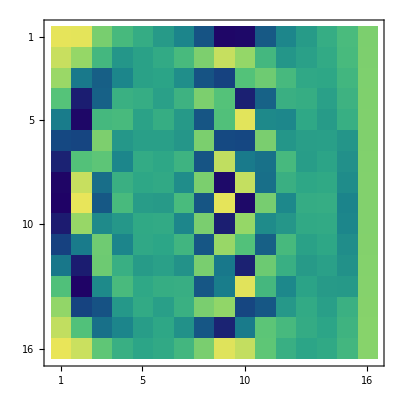

```mathematica
MatrixPlot[qp16//ArrayFlatten,ColorFunction->"BlueGreenYellow"]
```

```mathematica
U1 = GenMat[U, 16];
V1 = GenMat[V, 16];
G1 = GenMat[G, 16];
```